# Minimizing Functionals (RBF approach) J (y) = ∫(y(x) - f_0(x))^2+a f_1(|y’(x)|) + b f_2(|y’’(x)|) dx

## Defining functions f_1, f_2 , f_3 and weight constants a & b

```mathematica
Clear[x,x1,x2,x3,x4,L,f0,f1,f2,a,b,y,u];
f0[x_]=Sqrt[1+x^2] ;
f1[x_]=x^2;
f2[x_]=x^4;
(*Lagrangian constants*)
a=0.;
b=1.;
```

## Computing Lagrangian and left side of Euler-Lagrange equation

```mathematica
Print[Style["Lagrangian:",15,Blue]]
Lag[x1_,x2_,x3_,x4_]=(x2-f0[x1])^2+a f1[Sqrt[x3^2]]+b f2[Sqrt[x4^2]]
Print[Style["Real lagrangian",15,Blue]]
L[x_]=Lag[x,y[x],y'[x],y''[x]]
Ly[x_]=D[Lag[x1,x2,x3,x4], x2]/.x1->x/.x2->y[x]/.x3->y'[x]/.x4->y''[x];
Lyx[x_]=D[Lag[x1,x2,x3,x4], x3]/.x1->x/.x2->y[x]/.x3->y'[x]/.x4->y''[x];
Lyxx[x_]=D[Lag[x1,x2,x3,x4], x4]/.x1->x/.x2->y[x]/.x3->y'[x]/.x4->y''[x];
Print[Style["Left side of EL equation",15,Blue]]
el[x_]=Ly[x]-Lyx'[x]+Lyxx''[x]//FullSimplify (*left side of Euler-Lagrange equation*)
```

Lagrangian:

(-√(1+x1^2)+x2)^2+1. x3^2+1. x4^4

Real lagrangian

(-√(1+x^2)+y[x])^2+1. y'[x]^2+1. y''[x]^4

Left side of EL equation

-2. √(1+x^2)+2 y[x]+y''[x] (-2.+24. (y^(3)[x])^2+12. y''[x] y^(4)[x])

## Defining RBF to occupy and u(x) = Σc_j ϕ(|x-x_j|)

```mathematica
(*Number of RBF's*)
n=4;
(*Colocation points are linearly spaced*)
Col=Range[0,1,1/(n-1)];
(* Shape parameter *)
ϵ=0.5; 
(*RBF function*)
ϕ[r_]=Exp[-(ϵ r)^2];
Print[Style["u[x] function",15,Blue]]
u[x_]=∑_(j=1)^n Subscript[c, j] ϕ[√((x-Col[[j]])^2)]
(*Array with coefficients of u[x]*)
Coef=Table[Subscript[c, i],{i,n}];
```

u[x] function

ⅇ^(-0.25 x^2) c_1+ⅇ^(-0.25 (-1/3+x)^2) c_2+ⅇ^(-0.25 (-2/3+x)^2) c_3+ⅇ^(-0.25 (-1+x)^2) c_4

## Replacing y(x)->u(x) in EL equation and evaluation on interior points of domain

```mathematica
out1=el[x]/.y->u;
EL=RandomReal[{0,1},n-2];
For[i=1,i<=n-2,i++,
EL[[i]]=out1/.x->Col[[i+1]] //FullSimplify	
]
```

## Solving the non-linear system of equations: Approach 1, Newton Method

```mathematica
(*Setting random initial conditions*)
Print[Style["Initial conditions to occupy",15,Blue]]
lim=5.;
IC=Table[{Coef[[i]],RandomReal[{-lim,lim}]},{i,n}]
```

Initial conditions to occupy

{{c_1,-2.36667},{c_2,-4.16559},{c_3,0.455529},{c_4,2.73218}}

Vectorial function F[c̲] to solve

(-1+1. c_1+0.972604 c_2+0.894839 c_3+0.778801 c_4
-√2+0.778801 c_1+0.894839 c_2+0.972604 c_3+1. c_4
-2.10819+1.94521 c_1+2. c_2+1.94521 c_3+1.78968 c_4+(0.-0.459285 c_1-0.5 c_2-0.459285 c_3-0.347993 c_4) (-2.-2.21089 c_1^2-4.5 c_2^2-2.21089 c_3^2+c_1 (-8.02849 c_2-9.88927 c_3-9.57223 c_4)+c_2 (-8.02849 c_3-5.43532 c_4)-0.0810333 c_3 c_4+2.5159 c_4^2)
-2.4037+1.78968 c_1+1.94521 c_2+2. c_3+1.94521 c_4+(0.-0.347993 c_1-0.459285 c_2-0.5 c_3-0.459285 c_4) (-2.+2.5159 c_1^2-2.21089 c_2^2-4.5 c_3^2+c_2 (-8.02849 c_3-9.88927 c_4)+c_1 (-0.0810333 c_2-5.43532 c_3-9.57223 c_4)-8.02849 c_3 c_4-2.21089 c_4^2))

Solution

{c_1→7.36568,c_2→-10.1345,c_3→-1.4956,c_4→6.20116}

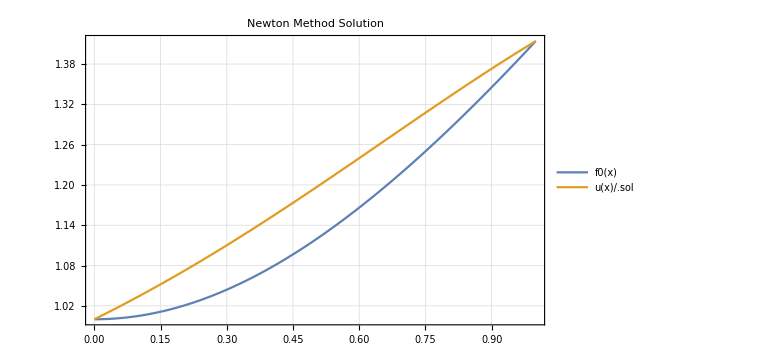

```mathematica
(*Vectorial function to which a solution must be found *)
F=Join[{u[0]-f0[0],u[1]-f0[1]},EL];
Print[Style["Vectorial function F[c̲] to solve" ,15,Blue]]
F//MatrixForm

(*Solve it*)
Print[Style["Solution",15,Blue]]
sol=FindRoot[F,IC,Method->{"Newton","UpdateJacobian"->1},MaxIterations->200]
Plot[{f0[x],u[x]/.sol},{x,0,1},PlotTheme->"Detailed",ImageSize->Large,PlotLabel->"Newton Method Solution"]
```

## Solving the non-linear system of equations: Approach 2, Dynamic System Applying the trick of made coefficients c_j dependant of time -> c_j(t)

### Dirty way to choose α_i to ensure convergence

```mathematica
(*Choosing Subscript[α, i]*)
Clear[F];
(*Redefining the vectorial function*)
Print[Style["Vectorial Function F[c̲] with factor α_i",15,Blue]]
alpha=Table[Subscript[α, i],{i,n}];
F=Join[{Subscript[α, 1](u[0]-f0[0]),Subscript[α, 2](u[1]-f0[1])},Table[Subscript[α, i] EL[[i-2]],{i,3,n}]];
F//MatrixForm

(*Jacobian*) 
DF=D[F,{Coef}];

(*Eigenvalues at stationary point*)
EVs=Eigenvalues[DF/.sol];

(*Find optimal values*)
opt=Minimize[{Max[Re[EVs]],Max[Re[EVs]]≥-10},alpha]

Print[Style["Values of α_i where real part of eigenvalues is negative",15,Blue]]
alpha/.opt[[2]]
Print[Style["Max Real part at that α_i values",15,Blue]]
opt[[1]]
```

Vectorial Function F[c̲] with factor α_i

((-1+1. c_1+0.972604 c_2+0.894839 c_3+0.778801 c_4) α_1
(-√2+0.778801 c_1+0.894839 c_2+0.972604 c_3+1. c_4) α_2
(-2.10819+1.94521 c_1+2. c_2+1.94521 c_3+1.78968 c_4+(0.-0.459285 c_1-0.5 c_2-0.459285 c_3-0.347993 c_4) (-2.-2.21089 c_1^2-4.5 c_2^2-2.21089 c_3^2+c_1 (-8.02849 c_2-9.88927 c_3-9.57223 c_4)+c_2 (-8.02849 c_3-5.43532 c_4)-0.0810333 c_3 c_4+2.5159 c_4^2)) α_3
(-2.4037+1.78968 c_1+1.94521 c_2+2. c_3+1.94521 c_4+(0.-0.347993 c_1-0.459285 c_2-0.5 c_3-0.459285 c_4) (-2.+2.5159 c_1^2-2.21089 c_2^2-4.5 c_3^2+c_2 (-8.02849 c_3-9.88927 c_4)+c_1 (-0.0810333 c_2-5.43532 c_3-9.57223 c_4)-8.02849 c_3 c_4-2.21089 c_4^2)) α_4)

{-0.0661585,{α_1→-0.672842,α_2→1.45195,α_3→-0.469053,α_4→0.539045}}

Values of α_i where real part of eigenvalues is negative

{-0.672842,1.45195,-0.469053,0.539045}

Max Real part at that α_i values

-0.0661585

### Time dependence trick

```mathematica
Print[Style["Function u[x]",15,Blue]]
ut[x_]=u[x]/.Table[Subscript[c, i]->Subscript[c, i][t],{i,n}]
ELt=EL/.Table[Subscript[c, i]->Subscript[c, i][t],{i,n}];
Coeft=Coef /.Table[Subscript[c, i]->Subscript[c, i][t],{i,n}];
Ft=F/.Table[Subscript[c, i]->Subscript[c, i][t],{i,n}]/.opt[[2]];
Print[Style["Vectorial Function F[c̲] to solve",15,Blue]]
Ft//MatrixForm
```

Function u[x]

ⅇ^(-0.25 x^2) c_1[t]+ⅇ^(-0.25 (-1/3+x)^2) c_2[t]+ⅇ^(-0.25 (-2/3+x)^2) c_3[t]+ⅇ^(-0.25 (-1+x)^2) c_4[t]

Vectorial Function F[c̲] to solve

(-0.672842 (-1+1. c_1[t]+0.972604 c_2[t]+0.894839 c_3[t]+0.778801 c_4[t])
1.45195 (-√2+0.778801 c_1[t]+0.894839 c_2[t]+0.972604 c_3[t]+1. c_4[t])
-0.469053 (-2.10819+1.94521 c_1[t]+2. c_2[t]+1.94521 c_3[t]+1.78968 c_4[t]+(0.-0.459285 c_1[t]-0.5 c_2[t]-0.459285 c_3[t]-0.347993 c_4[t]) (-2.-2.21089 c_1[t]^2-4.5 c_2[t]^2-2.21089 c_3[t]^2+c_1[t] (-8.02849 c_2[t]-9.88927 c_3[t]-9.57223 c_4[t])+c_2[t] (-8.02849 c_3[t]-5.43532 c_4[t])-0.0810333 c_3[t] c_4[t]+2.5159 c_4[t]^2))
0.539045 (-2.4037+1.78968 c_1[t]+1.94521 c_2[t]+2. c_3[t]+1.94521 c_4[t]+(0.-0.347993 c_1[t]-0.459285 c_2[t]-0.5 c_3[t]-0.459285 c_4[t]) (-2.+2.5159 c_1[t]^2-2.21089 c_2[t]^2-4.5 c_3[t]^2+c_2[t] (-8.02849 c_3[t]-9.88927 c_4[t])+c_1[t] (-0.0810333 c_2[t]-5.43532 c_3[t]-9.57223 c_4[t])-8.02849 c_3[t] c_4[t]-2.21089 c_4[t]^2)))

### Solving the dynamic system ∂c̲=F(c̲)

Dynamic System

(-0.672842 (-1+1. c_1[t]+0.972604 c_2[t]+0.894839 c_3[t]+0.778801 c_4[t])==c_1'[t]
1.45195 (-√2+0.778801 c_1[t]+0.894839 c_2[t]+0.972604 c_3[t]+1. c_4[t])==c_2'[t]
-0.469053 (-2.10819+1.94521 c_1[t]+2. c_2[t]+1.94521 c_3[t]+1.78968 c_4[t]+(0.-0.459285 c_1[t]-0.5 c_2[t]-0.459285 c_3[t]-0.347993 c_4[t]) (-2.-2.21089 c_1[t]^2-4.5 c_2[t]^2-2.21089 c_3[t]^2+c_1[t] (-8.02849 c_2[t]-9.88927 c_3[t]-9.57223 c_4[t])+c_2[t] (-8.02849 c_3[t]-5.43532 c_4[t])-0.0810333 c_3[t] c_4[t]+2.5159 c_4[t]^2))==c_3'[t]
0.539045 (-2.4037+1.78968 c_1[t]+1.94521 c_2[t]+2. c_3[t]+1.94521 c_4[t]+(0.-0.347993 c_1[t]-0.459285 c_2[t]-0.5 c_3[t]-0.459285 c_4[t]) (-2.+2.5159 c_1[t]^2-2.21089 c_2[t]^2-4.5 c_3[t]^2+c_2[t] (-8.02849 c_3[t]-9.88927 c_4[t])+c_1[t] (-0.0810333 c_2[t]-5.43532 c_3[t]-9.57223 c_4[t])-8.02849 c_3[t] c_4[t]-2.21089 c_4[t]^2))==c_4'[t]
c_1[0]==-2.36667
c_2[0]==-4.16559
c_3[0]==0.455529
c_4[0]==2.73218)

NDSolve::ndsz: At t == 0.126216, step size is effectively zero; singularity or stiff system suspected.

-Graphics-

Solution c_i[t] at t->∞

InterpolatingFunction::dmval: Input value {4000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {4000} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {4000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {4000} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {4000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {4000} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction :: dprec will be suppressed during this calculation.

{{InterpolatingFunction[{{0., 0.126216}}, <>][4000],InterpolatingFunction[{{0., 0.126216}}, <>][4000],InterpolatingFunction[{{0., 0.126216}}, <>][4000],InterpolatingFunction[{{0., 0.126216}}, <>][4000]}}

InterpolatingFunction::dmval: Input value {4000.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {4000.} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {4000.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {4000.} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {4000.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {4000.} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction :: dprec will be suppressed during this calculation.

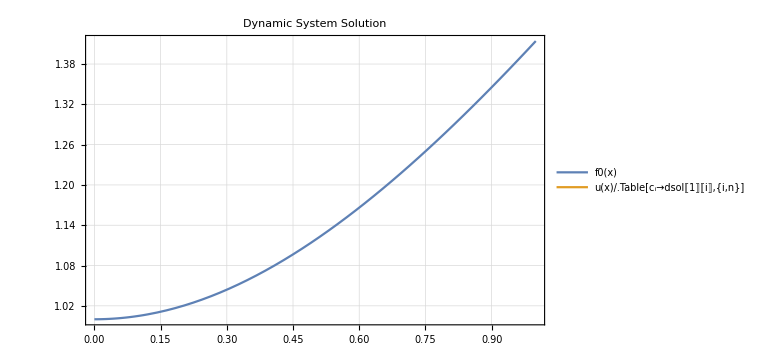

```mathematica
(*Solving the dynamic system with same IC as Newton Method approach*)
DSystem=Join[Table[Ft[[i]]==Subscript[c, i]'[t],{i,n}],Table[Subscript[c, i][0]==IC[[i]][[2]],{i,n}]];
Print[Style["Dynamic System",15,Blue]]
DSystem//MatrixForm

(*Solve it*)
Subscript[T, F]=4000;
s=NDSolve[DSystem,Coeft,{t,0,Subscript[T, F]},Method->"ImplicitRungeKutta"];

(*Plot of solutions Subscript[c, i][t]*)
Plot[Evaluate[Coeft/.s],{t,0,Subscript[T, F]},PlotTheme->"Detailed",ImageSize->Large,PlotLabel->"Stationary State"]
Print[Style["Solution c_i[t] at t->∞",15,Blue]]
dsol=Coeft/.s/.t->Subscript[T, F]

(*Plot of final solution*)
Plot[{f0[x],u[x]/.Table[Subscript[c, i]->dsol[[1]][[i]],{i,n}]},{x,0,1},PlotTheme->"Detailed",ImageSize->Large,PlotLabel->"Dynamic System Solution"]
```